```mathematica
(*========================= 初期化セル =========================*)
(*屈折率の関数を定義したノートブックを呼び出して評価*)
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
RefractiveIndexDefNotebookNames={
"Gehrsitz(2000)に基づくAlGaAsの組成比・温度・波長に依存した屈折率の導出.nb",(*nAlGaAs[(*Al組成比x*),(*温度T*),(*波長λ*)]*)
"SiO2とTiO2の室温の屈折率の導出.nb"};(*nSiO2RoomT[(*波長λ*)],nTiO2RoomT[(*波長λ*)]*)
Do[
nb=NotebookOpen[FileNameJoin[{NotebookDirectory[],RefractiveIndexDefNotebookName}]];
NotebookEvaluate[nb,EvaluationElements->"InitializationCell"];
NotebookClose[nb]
,{RefractiveIndexDefNotebookName,RefractiveIndexDefNotebookNames}]
(*真空の光学アドミッタンスY0=√(Subscript[ϵ, 0]/Subscript[μ, 0])*)Y0=2.6544*10^(-3);
(*光学アドミッタンスy*)y[N_]:=N*Y0
(*スネルの法則*)θ[Incidentθ_,IncidentN_,N_]:=ArcSin[(IncidentN/N)*Sin[Incidentθ]]
(*傾斜アドミッタンス*)η[polarization_,y_,θ_]:=Which[polarization=="P",y/Cos[θ],polarization=="S",y Cos[θ]]
(*位相シフト*)δ[λ_,N_,Thickness_,θ_]:=(2π/λ)*N* Thickness* Cos[θ]
(*特性マトリックス*)CharaMatrix[η_,δ_]:=({{Cos[δ], ⅈ (Sin[δ]/η)}, {ⅈ η Sin[δ], Cos[δ]}})
(*屈折率と層の厚さのリストから各層の特性マトリックスのリストを与える関数*)
CharaMatrixList[polarization_,Incidentθ_,IncidentN_,RefracIndexList_,ThicknessList_,λ_]:=
Table[CharaMatrix[
η[polarization,y[RefracIndexList[[i]]],θ[Incidentθ,IncidentN,RefracIndexList[[i]]]],δ[λ,RefracIndexList[[i]],ThicknessList[[i]],θ[Incidentθ,IncidentN,RefracIndexList[[i]]]]],{i,Length[RefracIndexList]}]
(*DBRを構成する各層の実部の屈折率のリストを与える関数*)
DBRNList[DBRPairNum_,N1_,N2_]:=Flatten[Table[{N1,N2},DBRPairNum]]
(*実部の屈折率のリストから目標波長におけるDBRの各層の厚さのリストを与える関数*)
DBRThicknessList[RefractiveIndexList_,TargetWavelength_]:=Table[TargetWavelength/(4*Re[RefractiveIndexList[[i]]]),{i,Length[RefractiveIndexList]}]
(*任意の行列のリストからそれらすべて内積した行列を与える関数*)
ListDot[list_]:=Apply[Dot,list];(*遅い*)
(*M[1]=First[CharaMatrixList];M[n_]:=M[n]=M[n-1].CharaMatrixList[[n]]*)
ListMultiplier1[list_,partitionwidth_: 4]:=Apply[Dot,Dot@@@Partition[list,UpTo[partitionwidth]]]
ListMultiplier2[list_,partitionwidth_: 2]:=NestWhile[Dot@@@Partition[#,partitionwidth,partitionwidth,1,{}]&,list,Dimensions[#][[1]]>1&][[1]]
(*Plot画像保存用関数*)
ExpVectorImg[plot_,name_]:=Export[FileNameJoin[{NotebookDirectory[],name<>".svg"}],plot,"SVG"]
ExpBitmapImg[plot_,name_]:=Export[FileNameJoin[{NotebookDirectory[],name<>".png"}],plot,"PNG",ImageResolution-> 600]
```

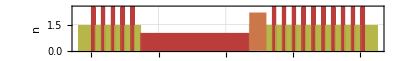

```mathematica
(*=================================================================*)
(*入射光の入射角度[deg]*)Incidentθdeg=0;       Incidentθ=Incidentθdeg*Degree;
(*入射光の偏光[P or S]*)Polari="S";
(*DBRミラーの目標波長[μm]*)TargetWL=0.81;
(*温度[K]*)Temperature=300;
(*入射媒質の複素屈折率*)IncidentN=nSiO2RoomT[(*波長λ*)λ]/.λ-> TargetWL;
(*基板媒質の複素屈折率*)SubstrateN=nSiO2RoomT[(*波長λ*)λ]/.λ-> TargetWL;
(*DBRミラーのペア数*)DBR1PairNum=5;DBR2PairNum=10;
(*DBR層の複素屈折率*)
DBRHighN=nTiO2RoomT[(*波長λ*)λ];
DBRLowN=nSiO2RoomT[(*波長λ*)λ];
(*複素屈折率のリスト*)
NList=Join[
DBRNList[DBR1PairNum,DBRHighN,DBRLowN],
{
1,
1.49,
2.1810
},
DBRNList[DBR2PairNum,DBRLowN,DBRHighN]
];
(*各層の厚さのリスト*)
ThicknessList=Join[
(1/4)*(TargetWL/Re[DBRNList[DBR1PairNum,DBRHighN,DBRLowN]]),
{
3*TargetWL,
(0/4)*(TargetWL/1.49),
(2/2)*(TargetWL/2.1810)
},
(1/4)*(TargetWL/Re[DBRNList[DBR2PairNum,DBRLowN,DBRHighN]])
]/.λ-> TargetWL;
(*
ThicknessList=Table[RandomVariate[NormalDistribution[ThicknessList[[i]],ThicknessList[[i]]*0.005]],{i,Length[ThicknessList]}]
*)
(*=================================================================*)
(*屈折率分布の可視化*)RefracIndexPlot=Show[
ListLinePlot[{{{-0.3,Re[IncidentN]},{0,Re[IncidentN]}},{{Last[Accumulate[ThicknessList]],Re[ReplaceAll[SubstrateN,λ->TargetWL] ]},{Last[Accumulate[ThicknessList]]+0.3,Re[ReplaceAll[SubstrateN,λ->TargetWL] ]}}},
PlotStyle->Directive[Opacity[0]],PlotTheme->{"Scientific","SansLabels"},Filling-> 0,FillingStyle->Automatic,ColorFunction->Function[{width,height},ColorData["DarkRainbow"][1-Mod[height,0.5]]],ColorFunctionScaling-> False],
RectangleChart[
Table[{Re[ThicknessList][[i]],ReplaceAll[Re[NList],λ->TargetWL] [[i]]},{i,Length[NList]}],
BarSpacing->None,PlotTheme->{"Scientific","SansLabels"},LabelingFunction->Automatic,ColorFunction->Function[{width,height},ColorData["DarkRainbow"][1-Mod[height,0.5]]],ColorFunctionScaling-> False
],
GridLines->Automatic,PlotRange->{0.,Automatic},PlotLabel->"Refractive index @ "<>ToString[TargetWL]<>" [μm]",FrameLabel->{"Distance from surface [μm]","n"},AspectRatio-> 1/(4*GoldenRatio),ImageSize-> Scaled[0.8]]
```

```mathematica
(*内積実行と振幅反射率，振幅透過率，エネルギー反射率，エネルギー透過率の計算*)
Print["特性マトリックスの全内積計算時間:",AbsoluteTiming[
M=ListMultiplier2[CharaMatrixList[Polari,Incidentθ,IncidentN,NList,ThicknessList,λ]];
][[1]],"[s]"]
Incidentη=η[Polari,y[IncidentN],Incidentθ];
Substrateη=η[Polari,y[SubstrateN],θ[Incidentθ,IncidentN,SubstrateN]];
{EiEs,HiEs}=M.{1,Substrateη};
ρ=(Incidentη-(HiEs/EiEs))/(Incidentη+(HiEs/EiEs));
τ=(2*Incidentη/(Incidentη+(HiEs/EiEs)))*(1/EiEs);
R=Abs[ρ]^2;
T=(Re[Substrateη]/Incidentη)*Abs[τ]^2;
```

特性マトリックスの全内積計算時間:0.108887[s]

```mathematica
(*透過率，反射率の可視化*)
PlotWLDelta=0.25;PlotCenter=TargetWL;
PlotWLmin=0.5(*PlotCenter-PlotWLDelta*);PlotWLmax=1.1(*PlotCenter+PlotWLDelta*);
{λmin}=FindArgMin[T,{λ,TargetWL}];
λminLine=Graphics[{Dashed,Line[{{λmin,0},{λmin,1}}]}];
λminText=Graphics[{Directive[FontSize-> Scaled[0.025]],Text["λ_min = "<>ToString[λmin]<>" μm",{λmin,0},{-1.1,-1.5},{0,1}]}];
TRPlot=Plot[{T(*,R,R+T*)},{λ,PlotWLmin,PlotWLmax},
PlotTheme->{(*"Monochrome",*)"Scientific","SansLabels"},PlotRange->{0-1*0.05,1+1*0.05},PlotLabels->Automatic,GridLines->Automatic,FrameStyle->Directive[FontSize-> Scaled[0.025]],PlotStyle->{Thickness[0.003]},FrameLabel->{"Wavelength [μm]",""},ImageSize-> Scaled[0.8]];
TRresult=Show[{TRPlot,λminLine,λminText}]
```

-Graphics-

```mathematica
Manipulate[Grid[{{"T","=",T},{"R","=",R},{"R+T","=",R+T}},Alignment->"."]/.λ-> a,{{a,PlotCenter,"波長 [um]"},0.3,1.,Appearance-> {"Labeled","Open"}}]
```

```mathematica
(*電場強度の描画*)
CharaMatrixListTargetWL=CharaMatrixList[
Polari,Incidentθ,IncidentN,ReplaceAll[NList,λ->TargetWL],ThicknessList,TargetWL];
Num=Length[ThicknessList];
MList=Table[ListMultiplier2[CharaMatrixListTargetWL[[i;;Num]]],{i,Num}];
En[i_]:=(MList[[i]].{1,Substrateη})[[1]]
Hn[i_]:=(MList[[i]].{1,Substrateη})[[2]]
(*進行波*)EnR[i_]:=(En[i]/2)+(Hn[i]/(2*η[Polari,y[NList[[i]]],θ[Incidentθ,IncidentN,NList[[i]]]]))
(*反射波*)EnL[i_]:=(En[i]/2)-(Hn[i]/(2*η[Polari,y[NList[[i]]],θ[Incidentθ,IncidentN,NList[[i]]]]))
zList=Prepend[Accumulate[ThicknessList],0];
Ez[z_]:=ReplaceAll[
If[z<0,
EnR[1]*Exp[-ⅈ*(δ[TargetWL,IncidentN,z,Incidentθ])]
+EnL[1]*Exp[+ⅈ*(δ[TargetWL,IncidentN,z,Incidentθ])],0]+
Sum[If[zList[[i]]≤ z<zList[[i+1]],
EnR[i]*Exp[-ⅈ*(δ[TargetWL,NList[[i]],z-zList[[i]],Incidentθ])]
+EnL[i]*Exp[+ⅈ*(δ[TargetWL,NList[[i]],z-zList[[i]],Incidentθ])],0],{i,Num}]+
If[Max[zList]≤ z,
EnR[Num]*Exp[-ⅈ*(δ[TargetWL,SubstrateN,z-Max[zList],Incidentθ]+(π/2))]
+EnL[Num]*Exp[+ⅈ*(δ[TargetWL,SubstrateN,z-Max[zList],Incidentθ]+(π/2))],0]
,λ->TargetWL]
```

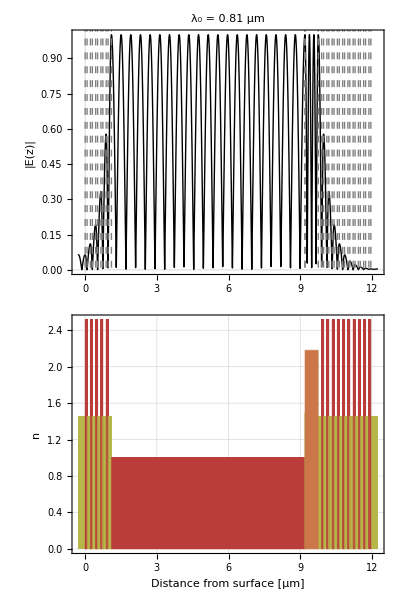

```mathematica
PlotFunc[z_]:=Abs@Ez[z]
MaxPlotFunc=Max[Table[Abs@PlotFunc[zi*(Max[zList]-Min[zList])/1000],{zi,1000}]];
MaxNList=Max[Re[ReplaceAll[NList,λ->TargetWL]]];
LinePlot=ListLinePlot[
Table[{{zList[[zi]],-MaxPlotFunc*1.2},{zList[[zi]],MaxPlotFunc*1.2}},{zi,Length[zList]}],
PlotStyle->Directive[Gray,Thickness[Tiny],Dashed]];
EzPlot=Plot[PlotFunc[z]/MaxPlotFunc,{z,-0.3,Max[zList]+0.3},
PlotStyle->Directive[Black,Thickness[Large]],
FrameLabel->{"","|E(z)|"},
PlotRange-> Full,PlotTheme->{"Scientific","SansLabels"},
ImageSize-> Scaled[0.8],AspectRatio-> 1/(4*GoldenRatio)];
(*Show[{RefracIndexPlot,EzPlot},PlotRange->{0,MaxNList}]*)
imagePadding={{70,10},{40,2}};
EzANDnPlot=Column[{
Show[{EzPlot,LinePlot},ImagePadding->imagePadding,
PlotLabel->"λ_0 = "<>ToString[TargetWL]<>" μm" ],
Show[RefracIndexPlot,ImagePadding->imagePadding,PlotLabel->""]},Spacings-> -2.5]
```

```mathematica
(*屈折率分布と透過率，反射率のPlot画像保存*)
ExpVectorImg[RefracIndexPlot,"RefracIndexPlot"]
ExpVectorImg[TRresult,"TRresult"]
ExpVectorImg[EzANDnPlot,"Ez_RefracIndex"]
```

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\RefracIndexPlot.svg

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\TRresult.svg

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\Ez_RefracIndex.svg

0.80085

{a→2.51874×10^-6,b→0.000490801}

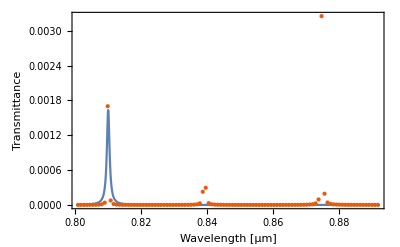

Q値：825.182

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\FitPlot.png

```mathematica
(*
Q値を求める（テスト版）：ある程度のQ値がないと以下の方法は失敗する．10ペア以上のDBRなど．Q値が高すぎても失敗する時がある．
*)
TArgMin1=FindArgMin[{T,0.8<λ<TargetWL},{λ,TargetWL}][[1]]
TArgMin2=FindArgMin[{T,λ>TargetWL},{λ,TargetWL}][[1]];
FitData=Transpose[ReplaceAll[{λ,T},λ-> Range[TArgMin1,TArgMin2,(TArgMin2-TArgMin1)/101]]];
FitDataListPlot=ListPlot[FitData,PlotTheme->{"Scientific","SansLabels"},PlotRange->All,PlotStyle->PointSize[Large]];
model= a PDF[CauchyDistribution[TargetWL,b],x];
fit=FindFit[FitData,{model,0.001>b>0},{a,{b,0.01}},x]
modelf=Function[{x},Evaluate[model/.fit]];
p=Plot[modelf[x],{x,TArgMin1,TArgMin2},PlotRange->All];
FitPlot=Show[{p,FitDataListPlot},PlotRange->All,Frame->True,FrameLabel->{"Wavelength [μm]","Transmittance"}]
Print["Q値：",Q=TargetWL/(2b)/.fit]
ExpBitmapImg[FitPlot,"FitPlot"]
```

```mathematica
(*分光光度計U-4000による透過率測定データを読み込みシミュレーション結果Tと重ねる*)
DataFileName="20191018_mirror.TXT";
TransExpData=Import[DataFileName,"Table"][[96;;-2]];
TransExpData[[All,1]]=TransExpData[[All,1]]*(1/1000);
TransExpData[[All,2]]=TransExpData[[All,2]]*(1/100)*12;
TransExpDataPlot=ListPlot[TransExpData,PlotStyle-> {Black}];
DATAonTRPlot=Show[{TRPlot,TransExpDataPlot},PlotRangeClipping->True]
ExpBitmapImg[DATAonTRPlot,"DATAonTRPlot"]
```

-Graphics-

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\DATAonTRPlot.png